```mathematica
Flatten[({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
Flatten[{{1,4,7},{2,5,8},{3,6,9}}]
```

```mathematica
FindPermutation[{1,2,3,4,5,6,7,8,9},{1,4,7,2,5,8,3,6,9}]
```

Cycles[{{2,4},{3,7},{6,8}}]

```mathematica
Det[({{a, b, c}, {d, e, f}, {g, h, i}})]==a Det[({{e, f}, {h, i}})]-b Det[({{d, f}, {g, i}})]+c Det[({{d, e}, {g, h}})]
```

```mathematica
Solve[1==(a x+b y+c z)^2,{a,b,c},Integers]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→ConditionalExpression[-1/x,((x|y|z|a|b|c)∈Integers&&y==0&&z==0&&x≥1)||((x|y|z|a|b|c)∈Integers&&y==0&&z==0&&x≤-1)]},{a→ConditionalExpression[1/x,((x|y|z|a|b|c)∈Integers&&y==0&&z==0&&x≥1)||((x|y|z|a|b|c)∈Integers&&y==0&&z==0&&x≤-1)]},{b→ConditionalExpression[(-1-a x)/y,((x|y|z|a|b|c)∈Integers&&z==0&&y≥1)||((x|y|z|a|b|c)∈Integers&&z==0&&y≤-1)]},{b→ConditionalExpression[(1-a x)/y,((x|y|z|a|b|c)∈Integers&&z==0&&y≥1)||((x|y|z|a|b|c)∈Integers&&z==0&&y≤-1)]},{c→ConditionalExpression[(-1-a x-b y)/z,((x|y|z|a|b|c)∈Integers&&z≥1)||((x|y|z|a|b|c)∈Integers&&z≤-1)]},{c→ConditionalExpression[(1-a x-b y)/z,((x|y|z|a|b|c)∈Integers&&z≥1)||((x|y|z|a|b|c)∈Integers&&z≤-1)]}}

```mathematica
Det[({{x, x+1, x+2, x+3}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})]
```

```mathematica
{{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}}
```

```mathematica
Permutations[Range[4]]
```

```mathematica
Map[#-1&,{{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3},{1,4,3,2},{2,1,3,4},{2,1,4,3},{2,3,1,4},{2,3,4,1},{2,4,1,3},{2,4,3,1},{3,1,2,4},{3,1,4,2},{3,2,1,4},{3,2,4,1},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,1,3,2},{4,2,1,3},{4,2,3,1},{4,3,1,2},{4,3,2,1}}]
```

{{0,1,2,3},{0,1,3,2},{0,2,1,3},{0,2,3,1},{0,3,1,2},{0,3,2,1},{1,0,2,3},{1,0,3,2},{1,2,0,3},{1,2,3,0},{1,3,0,2},{1,3,2,0},{2,0,1,3},{2,0,3,1},{2,1,0,3},{2,1,3,0},{2,3,0,1},{2,3,1,0},{3,0,1,2},{3,0,2,1},{3,1,0,2},{3,1,2,0},{3,2,0,1},{3,2,1,0}}

```mathematica
Map[Map[x+#&,#]&,%]
```

```mathematica
Map[{#}&,{{x,1+x,2+x,3+x},{x,1+x,3+x,2+x},{x,2+x,1+x,3+x},{x,2+x,3+x,1+x},{x,3+x,1+x,2+x},{x,3+x,2+x,1+x},{1+x,x,2+x,3+x},{1+x,x,3+x,2+x},{1+x,2+x,x,3+x},{1+x,2+x,3+x,x},{1+x,3+x,x,2+x},{1+x,3+x,2+x,x},{2+x,x,1+x,3+x},{2+x,x,3+x,1+x},{2+x,1+x,x,3+x},{2+x,1+x,3+x,x},{2+x,3+x,x,1+x},{2+x,3+x,1+x,x},{3+x,x,1+x,2+x},{3+x,x,2+x,1+x},{3+x,1+x,x,2+x},{3+x,1+x,2+x,x},{3+x,2+x,x,1+x},{3+x,2+x,1+x,x}}]
```

{{{x,1+x,2+x,3+x}},{{x,1+x,3+x,2+x}},{{x,2+x,1+x,3+x}},{{x,2+x,3+x,1+x}},{{x,3+x,1+x,2+x}},{{x,3+x,2+x,1+x}},{{1+x,x,2+x,3+x}},{{1+x,x,3+x,2+x}},{{1+x,2+x,x,3+x}},{{1+x,2+x,3+x,x}},{{1+x,3+x,x,2+x}},{{1+x,3+x,2+x,x}},{{2+x,x,1+x,3+x}},{{2+x,x,3+x,1+x}},{{2+x,1+x,x,3+x}},{{2+x,1+x,3+x,x}},{{2+x,3+x,x,1+x}},{{2+x,3+x,1+x,x}},{{3+x,x,1+x,2+x}},{{3+x,x,2+x,1+x}},{{3+x,1+x,x,2+x}},{{3+x,1+x,2+x,x}},{{3+x,2+x,x,1+x}},{{3+x,2+x,1+x,x}}}

```mathematica
Map[Join[#,{{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}}]&,%]
```

{{{x,1+x,2+x,3+x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{x,1+x,3+x,2+x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{x,2+x,1+x,3+x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{x,2+x,3+x,1+x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{x,3+x,1+x,2+x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{x,3+x,2+x,1+x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{1+x,x,2+x,3+x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{1+x,x,3+x,2+x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{1+x,2+x,x,3+x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{1+x,2+x,3+x,x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{1+x,3+x,x,2+x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{1+x,3+x,2+x,x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{2+x,x,1+x,3+x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{2+x,x,3+x,1+x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{2+x,1+x,x,3+x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{2+x,1+x,3+x,x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{2+x,3+x,x,1+x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{2+x,3+x,1+x,x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{3+x,x,1+x,2+x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{3+x,x,2+x,1+x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{3+x,1+x,x,2+x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{3+x,1+x,2+x,x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{3+x,2+x,x,1+x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}},{{3+x,2+x,1+x,x},{x5,x6,x7,x8},{x9,x10,x11,x12},{x13,x14,x15,x16}}}

```mathematica
Map[MatrixForm,%]
```

{(x | 1+x | 2+x | 3+x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(x | 1+x | 3+x | 2+x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(x | 2+x | 1+x | 3+x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(x | 2+x | 3+x | 1+x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(x | 3+x | 1+x | 2+x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(x | 3+x | 2+x | 1+x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(1+x | x | 2+x | 3+x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(1+x | x | 3+x | 2+x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(1+x | 2+x | x | 3+x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(1+x | 2+x | 3+x | x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(1+x | 3+x | x | 2+x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(1+x | 3+x | 2+x | x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(2+x | x | 1+x | 3+x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(2+x | x | 3+x | 1+x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(2+x | 1+x | x | 3+x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(2+x | 1+x | 3+x | x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(2+x | 3+x | x | 1+x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(2+x | 3+x | 1+x | x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(3+x | x | 1+x | 2+x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(3+x | x | 2+x | 1+x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(3+x | 1+x | x | 2+x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(3+x | 1+x | 2+x | x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(3+x | 2+x | x | 1+x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16),(3+x | 2+x | 1+x | x
x5 | x6 | x7 | x8
x9 | x10 | x11 | x12
x13 | x14 | x15 | x16)}

```mathematica
Map[Det,%]
```

```mathematica
{Det[({{x, 1+x, 2+x, 3+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{x, 1+x, 3+x, 2+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{x, 2+x, 1+x, 3+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{x, 2+x, 3+x, 1+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{x, 3+x, 1+x, 2+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{x, 3+x, 2+x, 1+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{1+x, x, 2+x, 3+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{1+x, x, 3+x, 2+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{1+x, 2+x, x, 3+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{1+x, 2+x, 3+x, x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{1+x, 3+x, x, 2+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{1+x, 3+x, 2+x, x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{2+x, x, 1+x, 3+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{2+x, x, 3+x, 1+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{2+x, 1+x, x, 3+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{2+x, 1+x, 3+x, x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{2+x, 3+x, x, 1+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{2+x, 3+x, 1+x, x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{3+x, x, 1+x, 2+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{3+x, x, 2+x, 1+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{3+x, 1+x, x, 2+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{3+x, 1+x, 2+x, x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{3+x, 2+x, x, 1+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})],Det[({{3+x, 2+x, 1+x, x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})]}
```

```mathematica
Det[({{x, 1+x, 2+x, 3+x}, {x5, x6, x7, x8}, {x9, x10, x11, x12}, {x13, x14, x15, x16}})]
```

```mathematica
Solve[1==3 x11 x14 x5+x x11 x14 x5-2 x12 x14 x5-x x12 x14 x5-3 x10 x15 x5-x x10 x15 x5+x12 x15 x5+x x12 x15 x5+2 x10 x16 x5+x x10 x16 x5-x11 x16 x5-x x11 x16 x5-3 x11 x13 x6-x x11 x13 x6+2 x12 x13 x6+x x12 x13 x6-x x12 x15 x6+x x11 x16 x6+3 x10 x13 x7+x x10 x13 x7-x12 x13 x7-x x12 x13 x7+x x12 x14 x7-x x10 x16 x7-2 x10 x13 x8-x x10 x13 x8+x11 x13 x8+x x11 x13 x8-x x11 x14 x8+x x10 x15 x8+3 x15 x6 x9+x x15 x6 x9-2 x16 x6 x9-x x16 x6 x9-3 x14 x7 x9-x x14 x7 x9+x16 x7 x9+x x16 x7 x9+2 x14 x8 x9+x x14 x8 x9-x15 x8 x9-x x15 x8 x9,x,Integers]
```

$Aborted

```mathematica
Solve[-1==3 x11 x14 x5+x x11 x14 x5-2 x12 x14 x5-x x12 x14 x5-3 x10 x15 x5-x x10 x15 x5+x12 x15 x5+x x12 x15 x5+2 x10 x16 x5+x x10 x16 x5-x11 x16 x5-x x11 x16 x5-3 x11 x13 x6-x x11 x13 x6+2 x12 x13 x6+x x12 x13 x6-x x12 x15 x6+x x11 x16 x6+3 x10 x13 x7+x x10 x13 x7-x12 x13 x7-x x12 x13 x7+x x12 x14 x7-x x10 x16 x7-2 x10 x13 x8-x x10 x13 x8+x11 x13 x8+x x11 x13 x8-x x11 x14 x8+x x10 x15 x8+3 x15 x6 x9+x x15 x6 x9-2 x16 x6 x9-x x16 x6 x9-3 x14 x7 x9-x x14 x7 x9+x16 x7 x9+x x16 x7 x9+2 x14 x8 x9+x x14 x8 x9-x15 x8 x9-x x15 x8 x9,x,Integers]
```

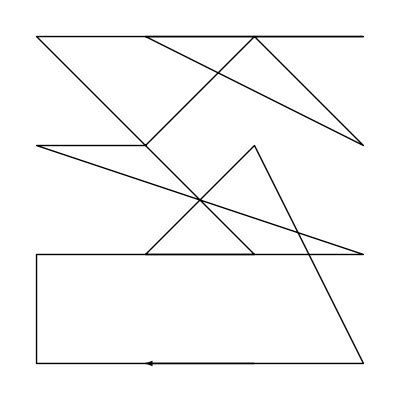
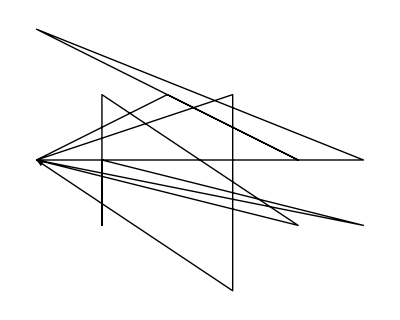
{(5 | 7 | 9 | 6
11 | 10 | 14 | 8
3 | 13 | 4 | 12
2 | 16 | 1 | 15),{-Graphics-,{{-2,0},{0,1},{2,0},{-2,2},{3,0},{-2,0},{2,-1},{-1,1},{-1,-1},{-1,0},{3,-1},{-2,0},{1,1},{1,-2},{-2,0}},-Graphics-}}

```mathematica
GM[({{5, 7, 9, 6}, {11, 10, 14, 8}, {3, 13, 4, 12}, {2, 16, 1, 15}})]
```

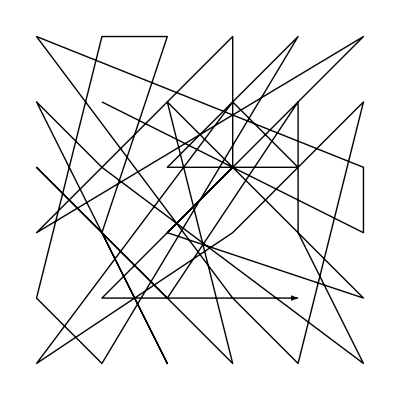
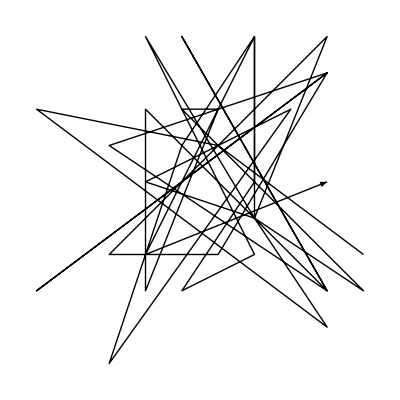
{(4 | 16 | 17 | 33 | 13 | 31
20 | 1 | 28 | 10 | 24 | 7
26 | 21 | 12 | 34 | 11 | 3
32 | 18 | 30 | 8 | 23 | 2
15 | 35 | 25 | 5 | 36 | 29
9 | 14 | 19 | 27 | 6 | 22),{-Graphics-,{{4,-2},{0,1},{-5,2},{3,-4},{1,-1},{1,4},{-2,-2},{-3,-2},{3,4},{1,-1},{-2,0},{2,2},{-3,-5},{-1,1},{1,4},{1,0},{-1,-3},{1,-2},{-2,4},{1,-1},{4,-3},{-1,2},{0,2},{-2,-3},{-2,2},{3,-3},{-1,4},{3,-3},{-3,1},{3,3},{-5,-3},{3,3},{0,-2},{-2,-2},{3,0}},-Graphics-}}

```mathematica
GM[Partition[Permute[Range[36],Cycles[{{1,8,22,36,29,30,21,14,32,19,33,4},{2,24,11,17,3,18,20,7,12,15,25,27,34,16},{5,28,9,31,6,35,26,13}}]],6]]
```

```mathematica
fwo[{x_,y_}]:=Piecewise[{{{x}, x>1}, {{x,y}, x≤1}}]
Monitor[Sort[Table[fwo[Block[{per=RandomPermutation[SymmetricGroup[36]]},{Abs[Det[Partition[Permute[Range[36],per],6]]],per}]],{i,1,30000000}],First[#1]<First[#2]&],i]
```

```mathematica
Out[2][[1]]
Out[2][[2]]
Out[2][[3]]
Out[2][[4]]
Out[2][[5]]
Out[2][[6]]
```

{0,Cycles[{{1,28,23,3,12,17,11,35,4,33,26,30,5,8,6,36,32,2,20,13,21,24,10,29,9,25,31,22,14,34},{7,27,19,15,16}}]}

{0,Cycles[{{1,33,31,8,21,13,29,16,19,12,14,23,4,15,36,3},{2,26,20,18,25,34,28},{5,9,17,30,27,11,6,32,22},{7,10,35}}]}

{0,Cycles[{{1,31,7,18,15,26,19,23},{2,30,27,5,36,3,29,20,9,32,16,10,12,24,33,14,6,35,11},{4,17,13,25,21,8,28},{22,34}}]}

{0,Cycles[{{1,32,5,20,12,14,25,17,23,30},{2,4,19,27,28,9,35,26,16,18,8,6,13,21,15,22,3,36,11,34,10,7,24,31,29,33}}]}

{0,Cycles[{{1,34,11,29,19,24,17,8,28,21,18,35,6,33,14,10,25,36,5,32,4},{2,22,16,26,7,27},{3,30,15,31},{12,23}}]}

{1,Cycles[{{1,31,22,32,7,26,36,16,28,4},{2,33,11,25,15,8,14,20,6,24,34,18,10},{3,30},{5,13,19,29},{9,21,27,17}}]}

```mathematica
Out[5][[1]]
Out[5][[2]]
Out[5][[3]]
```

{0,Cycles[{{1,25,16},{2,13,30,36,32,24,28,35,22},{3,19,11,12,29,23,26,8,33,18,20,31,9,27,17,5,6,21},{4,15,10,14}}]}

{0,Cycles[{{1,18,5,27,25,9,31,29,3,4,11,8,23,13,33,32,7,26,24,34,28},{2,6,15,30,36,17,19,10,14,20,16,21},{12,22}}]}

{0,Cycles[{{1,15,27,29,20,36,5,26,23,6,19,32,9,22,14},{2,10,11,30,13,34,4,35},{7,17},{8,24,16,12},{18,33,21,25},{28,31}}]}

```mathematica
Out[2][[1]]
```

{1,Cycles[{{1,36,19,18,32,33,23,21,30,20,34,26,35,15,24,7,25,5,9,13,27,2,22,12,31,28,14,3,10},{4,29,8,16,6,17}}]}

```mathematica
Out[2][[1]]
Out[2][[2]]
Out[2][[3]]
Out[2][[4]]
Out[2][[5]]
Out[2][[6]]
```

{0,Cycles[{{1,27,20,28,24,23,11,22,32,7,26,2,33,14,21,35,25,34,16,8},{3,12,19,6,31,15,13,10,5,17,29,36,4,18,30,9}}]}

{0,Cycles[{{1,3,24,34,13,32,10,11,30,26,18,12,2,6,33,15,20,22,28,19,31,14,16,23,4},{5,17,25,7,35,8},{9,29,36,21}}]}

{0,Cycles[{{1,12,24,36,33,14,21,22,31,17,20,2,8,32,34,7,30,6,10,27,19,28,35,9,29,15,26,3,13,16},{4,23,5,11,25,18}}]}

{0,Cycles[{{1,14,32,12,3,10,22,35,29,18,31,4,34,5,9,16},{2,26,25,23,15,20,6,11,24,8,27,17,28,30,33},{7,19},{21,36}}]}

{0,Cycles[{{1,27,16,31,13,29,11,30,15,34,8,7,32,26,2,35,21,14,28,23},{3,22,24,36,20,4,17,33,12},{5,10,18,6},{9,25}}]}

{0,Cycles[{{1,35,11,33,14,6,19,15,21,4,23,22,7,31,8,25,9,10,12,18,29,36,34,5,3,26},{2,30,28,32},{13,24,17,20}}]}

```mathematica
Out[2][[1]]
Out[2][[2]]
```

{0,Cycles[{{2,13,33,14,11,34,9,17,6,29,31,23,24,26,15,10,35,4,5},{3,28,22,32,21,30,12,36,8,16,19,20,7},{18,25}}]}

{0,Cycles[{{1,34,15,3,5,23,14,27,18,33,4,10,2,29,7,36,20},{6,12,22,32,9,26,24,17,8,25,21,16,31,13,35,11,28}}]}

```mathematica
Out[4][[1]]
Out[4][[2]]
Out[4][[3]]
```

{0,Cycles[{{1,29,35,20,2,14,31,36,18,7,23,10,32,9,33,16,8,27,28,11,12,19,17,34,4,13,22,15,21,6,30},{3,24},{5,26,25}}]}

{0,Cycles[{{1,12,20,32,23,19,10,22,26,15,27,33,35,31,9,6,7,14,8,36,30,13,17,25,16,29,3,34,18,21,28,2,4,5,11,24}}]}

{0,Cycles[{{1,25,28,29,9,21,22,17,20,10,19,14,30,35,36},{2,34,8,16,6,13,3,7,27,26,11,12,24,4,18,31,23,32,5,33,15}}]}

```mathematica
Out[2][[1]]
Out[2][[2]]
Out[2][[3]]
```

{0,Cycles[{{1,14,28,35,36,34,10,24,8,12,33,6,11,22,18,20,7,16,32,21,26,27,5,15,25,30,29,17,2,3,13,4},{9,31}}]}

{0,Cycles[{{1,19,36,20,8,33,22,14,5,9,4,6,30,29,25,16,17,18,32,12,15,13,11,21,35,31,7,23,3},{2,28,10,34,27,26,24}}]}

{1,Cycles[{{1,27,13,30,2,22,6,23,32,24,35,29,5,15,20,25,10,17,26,28,8,12,3,36,31,34,14},{4,16},{7,21,19},{9,18,33,11}}]}

```mathematica
Out[2][[1]]
Out[2][[2]]
Out[2][[3]]
Out[2][[4]]
```

{0,Cycles[{{1,32,20,29,2,31,28,14,5,24,26,21,7,3},{4,8,22,18,25},{6,30,36,12,10,13},{9,33,17,15,11,27,34,23,35,16}}]}

{0,Cycles[{{1,2,27,21,14,25,3,31,26,34,23},{4,17,32,22,24,15,19,35,20,30,16,28,33,29,7,12,9,8,11,18,36,13,5,6}}]}

{0,Cycles[{{1,10,33,27,11,29,9,24,21,34,17,31,15,7,23,35},{2,6,12,13,16,8,25,20,26,18,5,28,4},{3,19,32,14},{22,36}}]}

{0,Cycles[{{1,20,6,23,26,4,2,36,9,18,22,35,17,30,31,8,33},{3,5,28,27,14,10,12,13,29,15,7,19,34,16,11,24,25,32}}]}

```mathematica
Out[2][[1]]
Out[2][[2]]
Out[2][[3]]
Out[2][[4]]
Out[2][[5]]
```

{0,Cycles[{{1,32,20,29,2,31,28,14,5,24,26,21,7,3},{4,8,22,18,25},{6,30,36,12,10,13},{9,33,17,15,11,27,34,23,35,16}}]}

{0,Cycles[{{1,2,27,21,14,25,3,31,26,34,23},{4,17,32,22,24,15,19,35,20,30,16,28,33,29,7,12,9,8,11,18,36,13,5,6}}]}

{0,Cycles[{{1,10,33,27,11,29,9,24,21,34,17,31,15,7,23,35},{2,6,12,13,16,8,25,20,26,18,5,28,4},{3,19,32,14},{22,36}}]}

{0,Cycles[{{1,20,6,23,26,4,2,36,9,18,22,35,17,30,31,8,33},{3,5,28,27,14,10,12,13,29,15,7,19,34,16,11,24,25,32}}]}

{2}

```mathematica
Out[2][[1]]
Out[2][[2]]
Out[2][[3]]
Out[2][[4]]
Out[2][[5]]
```

{0,Cycles[{{1,30,29,36,28,14,2},{3,7,33,21,32,13,19,24,22,10,4,16,18,34,9,5,11,8,17,35,15,25},{6,27,31,20},{23,26}}]}

{0,Cycles[{{1,7,35,15,22,20,6,33,29,32,10,17},{2,30,16,23,12,4,28,18,9,3,25,8,14,34,11,27,19,31,26,13},{21,24}}]}

{0,Cycles[{{2,5,14,19,16,22,10,11,4,15,26,7,6,18,31,28,34,32,12,35,20,25,8,24,27,3,9,23,13,29,36,21,30,17}}]}

{0,Cycles[{{1,12,25,6,5,11,14,20,23,31,36,29,34,22,2,33,35,4,15},{3,18,19,32,26,27,17,9,7,24,10,13},{8,16},{28,30}}]}

{0,Cycles[{{1,3,10,25,34,14,26,31,22,2,8,32,27,5,9,24,30,28,16,33,18,11,15,7,35,17,6,4,21,19,36,20,12,23},{13,29}}]}

```mathematica
Out[2][[1]]
```

{0,Cycles[{{1,25,24,20,3},{2,29,9,35,23,30,22,16,15,32,21,10,31,5,17,28,34,11,26,27,19,4,36,12,18},{6,8,14,33,7,13}}]}

{1,Cycles[{{1,21},{2,25,8,5,9,24,14,13},{3,10,31,22,11,6,4,18,34,33},{7,27},{12,15,32,29,16,23,35,30,36,17,26,19,28}}]}

```mathematica
Out[2][[1]]
Out[2][[2]]
```

{0,Cycles[{{1,22,4,12,33,32,13,23,20,31,14,21,11,2,34,16,17,5,8,35,6,29},{3,36,25,10,15,24,9,30,18,19},{7,28,26}}]}

{1,Cycles[{{1,14,17,12,29,5},{2,20,23,27,34,35,11,22,18,16,7,10,4,13,9,33,30,31,6,21,25,36,3,32,24},{8,19},{15,26,28}}]}

```mathematica
Out[2][[1]]
```

{1,Cycles[{{1,4,36,15,25,10,29,33,11,28,8,2,14,7,24,21,5,31,16,32,27},{3,17,20},{6,19,34,22,12,9,18,23,35,26,30}}]}

```mathematica
Out[2][[1]]
Out[2][[2]]
Out[2][[3]]
```

{0,Cycles[{{1,25,7,35,32,12,13,9},{2,14,34,24,21,31,11,20,17,6,26,10,3,36,23,4,28,8},{5,22,15},{18,30,33,29,19}}]}

{0,Cycles[{{1,14,10,4,21,33,3,15,6,31},{2,34},{5,36,11,29,17,12,30,26,25,19,28,18,13,27,8,23,22,16},{7,24},{9,32},{20,35}}]}

{0,Cycles[{{1,16,20,33,11,22,7,34,27,32,3,15,21,23,26,8,13,9,31,35,36,17,28,6},{2,29},{4,14,18,24,10,25},{5,19,12,30}}]}

```mathematica
Out[2][[1]]
```

{0,Cycles[{{1,16,6,28,25,13,27,8,9,32,30,18,11,35,10,20,22,24,5,2,15,21,26,31,3,12,14,29,36,34,33,7},{4,17,23,19}}]}

```mathematica
Out[4][[1]]
Out[4][[2]]
```

{0,Cycles[{{1,28,32,19,30,23,14,34,18,11,12,16,31,3,21,10,29,20,33,2,24,17,15,7,9,27,13,25},{4,6,36,5,35},{8,26,22}}]}

{0,Cycles[{{1,22,11,3,33,27,18,9,6,7,34,25,19,12,24,21,4,13,5,35},{2,10,26,8,32,14,31,15,29,36,30,23},{16,20}}]}

```mathematica
First[Out[2]]
```

{0,Cycles[{{1,4,30,7,36,18,31,24,12,2,6,34,15,27,5,9,32,3},{8,35,11,23},{10,16,28},{13,14,33,17,20,26,19,22,29,25}}]}

```mathematica
First[Out[6]]
```

{0,Cycles[{{1,8,19,17,25,34,18,31,26,4,27,6,20,2,12,22,9,10,16,23,35,30,21,11,24,5,28,15,32,14,3,13,29,7},{33,36}}]}

```mathematica
Table[Out[2][[i]],{i,1,5}]
```

{{0,Cycles[{{1,30,14,23,32,15,12,11,7,5,26,22,16,8,24,9,19,2,6,4,29,31},{10,13,25,17,20,34,33,21,28,36,18}}]},{0,Cycles[{{1,21,7,30,15,31,23,12,24,5},{2,4,17},{3,14,22,16,6,27,18,11,25,19,13},{9,26,10,28},{20,36,29,34,33,35}}]},{0,Cycles[{{1,31,19,23,2,3,14,29,6,20,7,10,30,13,12,27,32,4,8,17,35,24,9,26,11,16,18},{5,22},{15,33,34,36},{21,28,25}}]},{0,Cycles[{{1,29,10,21,18,28,2,20,31,22,3,13,33,4,8,24,30,25},{5,11,35},{6,16,26,9,7,23,15,12,19,36,17,34,32,27}}]},{0,Cycles[{{1,26,2,4,35,24,21,20,29,25,17,6,32,3,18},{5,15,36,31,28,33,7,13,30,10,16,27,12,23,22,11,14,34,9,19,8}}]}}

```mathematica
First[Out[2]]
```

{0,Cycles[{{1,2,16,24,32,7,9,8,22,36,21,29,23,6,18,33,26,4,25,34,19,17,28,30,11,20,12,15,35,31},{3,14},{10,13,27}}]}

```mathematica
First[Out[9]]
```

{0,Cycles[{{1,32,15,3,4,34,27,30,19,6,26,10,28,14,17,21,11,25,35,16,8,31,23,7,2,29,33,36,13,9,12},{5,22,24,18}}]}

```mathematica
Out[2][[1]]
Out[2][[2]]
```

{0,Cycles[{{1,36,20,31,5,32,34,33,11},{2,3,35,22,16,23,6,24,12,9,18,8,28},{4,17,27,10,29,30,19},{7,25,26,15}}]}

{0,Cycles[{{1,33,30,31,6,5,4,10,8,20},{2,27,25,36,24,23,14,12,7,9},{3,28,16,35,32},{11,29,34,22,19,13,15,18,21,26}}]}

```mathematica
First[Out[4]]
```

{1,Cycles[{{1,9,11,8,4,12,5,29,17,36,22,23,20,3,35,10,30,28,26},{2,18,13,6,33,34,32,15,14,25,19},{7,27,31,21,16}}]}

```mathematica
First[Out[12]]
```

{0,Cycles[{{1,6,30,12,23,14,8,16,2,28,15},{4,34,32,19,7,29,25},{5,18,26,17},{9,11},{10,21},{13,22,20},{24,33,35,31,36,27}}]}

```mathematica
First[Out[2]]
```

{0,Cycles[{{1,19,13,36,28,27,18},{2,21,26,25,14,8,23,10,22},{3,31,32,34,29,9,20,4,7,15,17,16,6,33,35,11,24},{5,30}}]}

```mathematica
First[Out[19]]
```

{0,Cycles[{{1,15,30,6},{2,10,21,8,24,29,25,4,34,31,28,23},{3,35},{5,17,9,14,18,19},{7,33,12,16,32,36,22,26},{11,27}}]}

```mathematica
19264
```

```mathematica
First[Out[12]]
```

{0,Cycles[{{1,16,28,32,31,13,7,30,9,18,25,6,11,33,19,23,10,34,29,14,5,20,21,12,17},{2,36,27,4,26,24,3,15,22,8}}]}

```mathematica
First[Out[9]]
```

{0,Cycles[{{1,31,8,11,22,5,23,12,30,36,14,13,28,29,34,6,9,15,26,27,10,20,3,25,17,4,7,21,32},{2,16,19,35,18},{24,33}}]}

```mathematica
First[Out[5]]
```

{0,Cycles[{{1,34,17,14,33,27,28,32,8,11,18,9,25,3,15,31,6,29,23,4,36,26,7,10,5,19,2,20},{12,16,21},{13,24,30,35}}]}

```mathematica
First[Out[160]]
```

{0,Cycles[{{1,8,22,36,29,30,21,14,32,19,33,4},{2,24,11,17,3,18,20,7,12,15,25,27,34,16},{5,28,9,31,6,35,26,13}}]}

```mathematica
First[Out[268]]
```

{0,Cycles[{{1,2,28,15,14,8,10,25,7,34,35,29,5,32,18,16,36,17,20,9,31,12,33,24,21,27,30,11,3},{4,26,19,13,6},{22,23}}]}

```mathematica
985579871655589/10000000//N
```

9.8558×10^7

```mathematica
{Min[Flatten[Out[15]]],Mean[Flatten[Out[15]]]}
```

{21,985579871655589/10000000}

{Min[0,Cycles[{{1,34,17,14,33,27,28,32,8,11,18,9,25,3,15,31,6,29,23,4,36,26,7,10,5,19,2,20},{12,16,21},{13,24,30,35}}]],(985380440259539+Cycles[{{1,34,17,14,33,27,28,32,8,11,18,9,25,3,15,31,6,29,23,4,36,26,7,10,5,19,2,20},{12,16,21},{13,24,30,35}}])/10000001}

{12,12323962969829/125000}

{130,98475149041801/1000000}

{8,9871594134481/100000}

{149,49258364096617/500000}

{65,98456634272523/1000000}

{76,157970604471/1600}

{89,6146215386547/62500}

{75,24634369940151/250000}

{22,98483345830331/1000000}

{670,9908915910693/100000}

{1692,9865822449003/100000}

{250,1237031062623/12500}

{450,2460451837249/25000}

{375,2461345307727/25000}

{1725,493145906041/5000}

{478,1976650290239/20000}

{268,614378299781/6250}

{138,1973806383991/20000}

{224,307339070903/3125}

{2246,9869007744417/100000}

{896,2449976693093/25000}

{792,2470701145047/25000}

{1919,9861956734411/100000}

{144,1976100118071/20000}

{852,9848960694263/100000}

{275,9849796669551/100000}

{261,4963067085393/50000}

{598,2473386704161/25000}

{491,984574412601/10000}

{478,2479904944057/25000}

{938,4913995051037/50000}

{127,98708501629/1000}

{1521,9865583401653/100000}

{2201,2467602076039/25000}

{628,1963469203293/20000}

{1165,2471060524041/25000}

{364,9846063705463/100000}

{1086,9804398282147/100000}

{390,9841355774503/100000}

{638,2456516981779/25000}

{1968,986244338777/10000}

{150,1973361213507/20000}

{462,4934164635877/50000}

{429,9855489770907/100000}

{770,2470097421583/25000}

{411,394691336963/4000}

{2680,2468255127981/25000}

{3531,9906844024859/100000}

{11,9867021882249/100000}

{153,2449685107039/25000}

{598,9864543576431/100000}

{36,2477394856927/25000}

{664,4936120023339/50000}

{2059,396003268351/4000}

{1372,2463774100379/25000}

{2978,9808788946981/100000}

{160,2475690830011/25000}

{928,4917333051491/50000}

{238,4923836963339/50000}

{336,9788126364787/100000}

{168,611762164217/6250}

{996,9836402925657/100000}

{1404,2462441333197/25000}

{1873,1960133832163/20000}

{1259,2462455823741/25000}

{1024,9847088351121/100000}

{8,9881290231163/100000}

{580,1234458908603/12500}

{1042,9849564817453/100000}

{190,4936507322281/50000}

{43,4899123613629/50000}

{81,9852193341347/100000}

{956,494233078557/5000}

{Min[0,Cycles[{{1,8,22,36,29,30,21,14,32,19,33,4},{2,24,11,17,3,18,20,7,12,15,25,27,34,16},{5,28,9,31,6,35,26,13}}]],(9886591701540+Cycles[{{1,8,22,36,29,30,21,14,32,19,33,4},{2,24,11,17,3,18,20,7,12,15,25,27,34,16},{5,28,9,31,6,35,26,13}}])/100001}

```mathematica
{4792,497992178487/5000}
```

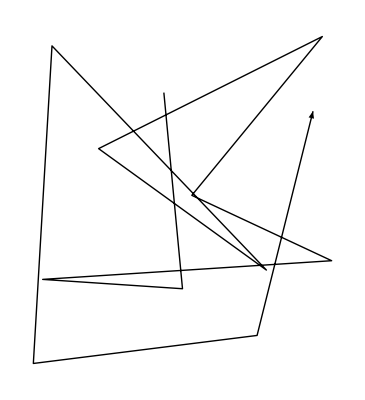
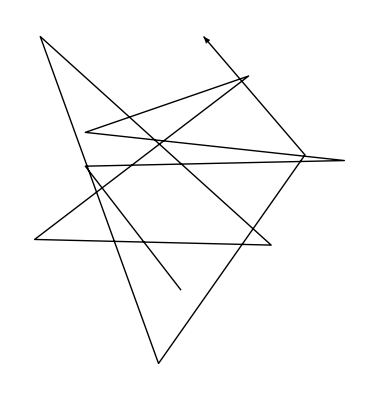
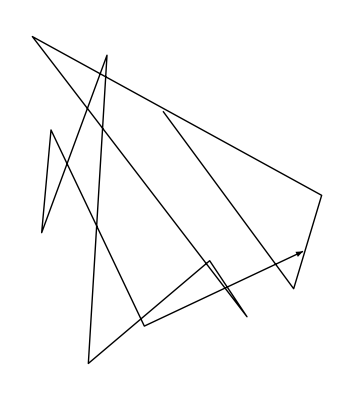
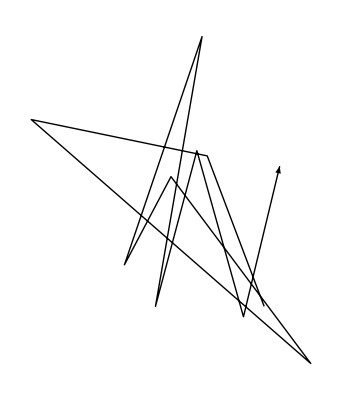
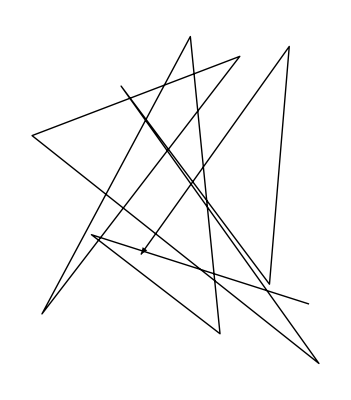
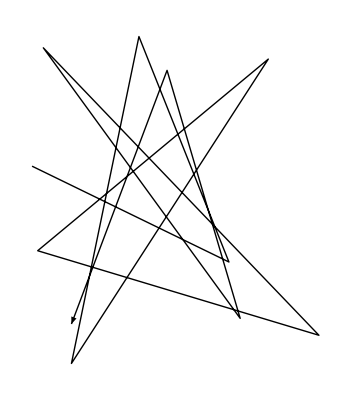
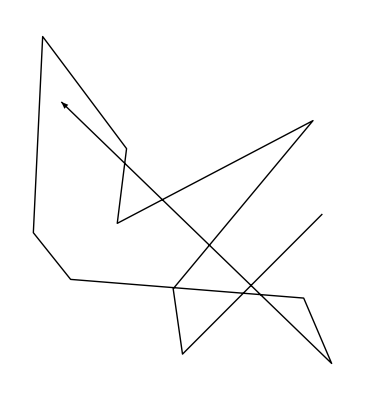
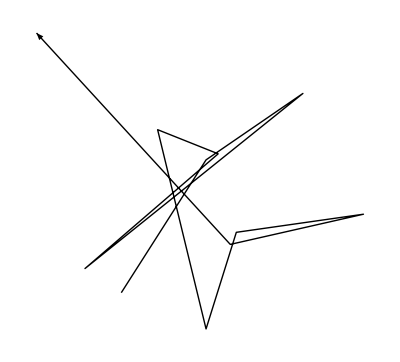
{Cycles[{{1,15,30,6},{2,10,21,8,24,29,25,4,34,31,28,23},{3,35},{5,17,9,14,18,19},{7,33,12,16,32,36,22,26},{11,27}}],{-Graphics-,{{2,-21},{-15,1},{31,2},{-15,7},{14,17},{-24,-12},{18,-13},{-23,24},{-2,-34},{24,3},{6,24}},-Graphics-}}
{Cycles[{{1,16,28,32,31,13,7,30,9,18,25,6,11,33,19,23,10,34,29,14,5,20,21,12,17},{2,36,27,4,26,24,3,15,22,8}}],{-Graphics-,{{14,-19},{3,10},{-31,17},{23,-30},{-4,6},{-13,-11},{2,33},{-7,-19},{1,11},{10,-21},{17,8}},-Graphics-}}
{Cycles[{{1,31,8,11,22,5,23,12,30,36,14,13,28,29,34,6,9,15,26,27,10,20,3,25,17,4,7,21,32},{2,16,19,35,18},{24,33}}],{-Graphics-,{{-22,7},{13,-10},{-3,30},{-15,-28},{20,26},{-21,-8},{29,-23},{-20,28},{15,-20},{2,24},{-15,-21}},-Graphics-}}
{Cycles[{{1,34,17,14,33,27,28,32,8,11,18,9,25,3,15,31,6,29,23,4,36,26,7,10,5,19,2,20},{12,16,21},{13,24,30,35}}],{-Graphics-,{{-15,-15},{-1,7},{15,18},{-21,-11},{1,8},{-9,12},{-1,-21},{4,-5},{25,-2},{3,-7},{-29,28}},-Graphics-}}
{Cycles[{{1,8,22,36,29,30,21,14,32,19,33,4},{2,24,11,17,3,18,20,7,12,15,25,27,34,16},{5,28,9,31,6,35,26,13}}],{-Graphics-,{{16,-11},{11,15},{-34,-25},{24,26},{-22,-9},{30,-14},{-26,8},{7,20},{-5,-1},{7,-26},{13,25}},-Graphics-}}
{Cycles[{{1,2,28,15,14,8,10,25,7,34,35,29,5,32,18,16,36,17,20,9,31,12,33,24,21,27,30,11,3},{4,26,19,13,6},{22,23}}],{-Graphics-,{{30,-10},{-10,5},{3,-16},{-22,-3},{30,20},{-19,-16},{22,9},{-27,14},{18,-1},{-8,-17},{16,16}},-Graphics-}}

```mathematica
Map[GM[Last[#]]&,{{0,Cycles[{{1,15,30,6},{2,10,21,8,24,29,25,4,34,31,28,23},{3,35},{5,17,9,14,18,19},{7,33,12,16,32,36,22,26},{11,27}}]},
{0,Cycles[{{1,16,28,32,31,13,7,30,9,18,25,6,11,33,19,23,10,34,29,14,5,20,21,12,17},{2,36,27,4,26,24,3,15,22,8}}]},
{0,Cycles[{{1,31,8,11,22,5,23,12,30,36,14,13,28,29,34,6,9,15,26,27,10,20,3,25,17,4,7,21,32},{2,16,19,35,18},{24,33}}]},
{0,Cycles[{{1,34,17,14,33,27,28,32,8,11,18,9,25,3,15,31,6,29,23,4,36,26,7,10,5,19,2,20},{12,16,21},{13,24,30,35}}]},
{0,Cycles[{{1,8,22,36,29,30,21,14,32,19,33,4},{2,24,11,17,3,18,20,7,12,15,25,27,34,16},{5,28,9,31,6,35,26,13}}]},
{0,Cycles[{{1,2,28,15,14,8,10,25,7,34,35,29,5,32,18,16,36,17,20,9,31,12,33,24,21,27,30,11,3},{4,26,19,13,6},{22,23}}]}}]//Column
```